```mathematica
ClearAll["Global`*"]
```

# Analytical expressions for stationary probability distribution and stochastic potential of autoc.-FB

How does the stationary probability of a Fokker-Plank associated with the autocatalytic feedback loop change if I change the cooperativity index of the Hill function?

## Analytical expression for the stochastic potential

Which is basically the exponent of the probability function but - nicely - does not have normalization constants in the way.

#### Potential depending on changing Hill’s exponent

This is for

```mathematica
0.5*Log[σ]-(1/σ)*∫(k+a*(x^n)/(1+x^n)-x)ⅆx
```

-(k x-x^2/2+(a x^(1+n) Hypergeometric2F1[1,(1+n)/n,1+(1+n)/n,-x^n])/(1+n))/σ+0.5 Log[σ]

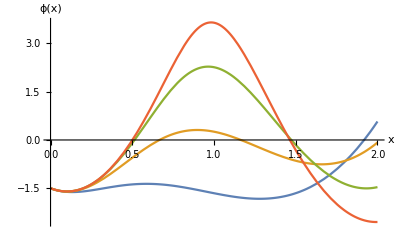

```mathematica
σ=0.05;
k=0.1;
a={1.9};
n={2,3,5,8};
Plot[{-(k x-x^2/2+(a x^(1+n[[1]]) Hypergeometric2F1[1,(1+n[[1]])/n[[1]],1+(1+n[[1]])/n[[1]],-x^n[[1]]])/(1+n[[1]]))/σ+0.5 Log[σ],-(k x-x^2/2+(a x^(1+n[[2]]) Hypergeometric2F1[1,(1+n[[2]])/n[[2]],1+(1+n[[2]])/n[[2]],-x^n[[2]]])/(1+n[[2]]))/σ+0.5 Log[σ],-(k x-x^2/2+(a x^(1+n[[3]]) Hypergeometric2F1[1,(1+n[[3]])/n[[3]],1+(1+n[[3]])/n[[3]],-x^n[[3]]])/(1+n[[3]]))/σ+0.5 Log[σ],-(k x-x^2/2+(a x^(1+n[[4]]) Hypergeometric2F1[1,(1+n[[4]])/n[[4]],1+(1+n[[4]])/n[[4]],-x^n[[4]]])/(1+n[[4]]))/σ+0.5 Log[σ]},{x,0,2},AxesLabel->{Style["x",FontSize->{16}],Style["ϕ(x)",FontSize->{16}]}]
```

## Expression for the probability function

Normalization constants

```mathematica
N1 =NIntegrate[Exp[-(-(k x-x^2/2+(a x^(1+n[[1]]) Hypergeometric2F1[1,(1+n[[1]])/n[[1]],1+(1+n[[1]])/n[[1]],-x^n[[1]]])/(1+n[[1]]))/σ+0.5 Log[σ])],{x,0,3}];
N2 = NIntegrate[Exp[-(-(k x-x^2/2+(a x^(1+n[[2]]) Hypergeometric2F1[1,(1+n[[2]])/n[[2]],1+(1+n[[2]])/n[[2]],-x^n[[2]]])/(1+n[[2]]))/σ+0.5 Log[σ])],{x,0,3}];
N3 = NIntegrate[Exp[-(-(k x-x^2/2+(a x^(1+n[[3]]) Hypergeometric2F1[1,(1+n[[3]])/n[[3]],1+(1+n[[3]])/n[[3]],-x^n[[3]]])/(1+n[[3]]))/σ+0.5 Log[σ])],{x,0,3}];
N4 = NIntegrate[Exp[-(-(k x-x^2/2+(a x^(1+n[[4]]) Hypergeometric2F1[1,(1+n[[4]])/n[[4]],1+(1+n[[4]])/n[[4]],-x^n[[4]]])/(1+n[[4]]))/σ+0.5 Log[σ])],{x,0,3}];
```

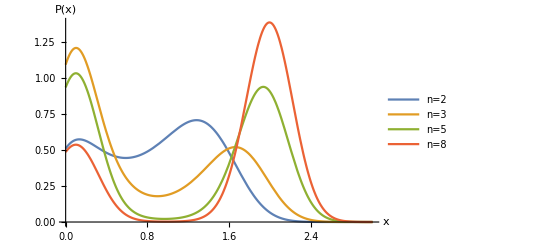

```mathematica
Plot[{(1/N1)*Exp[-(-(k x-x^2/2+(a x^(1+n[[1]]) Hypergeometric2F1[1,(1+n[[1]])/n[[1]],1+(1+n[[1]])/n[[1]],-x^n[[1]]])/(1+n[[1]]))/σ+0.5 Log[σ])],(1/N2)*Exp[-(-(k x-x^2/2+(a x^(1+n[[2]]) Hypergeometric2F1[1,(1+n[[2]])/n[[2]],1+(1+n[[2]])/n[[2]],-x^n[[2]]])/(1+n[[2]]))/σ+0.5 Log[σ])],(1/N3)*Exp[-(-(k x-x^2/2+(a x^(1+n[[3]]) Hypergeometric2F1[1,(1+n[[3]])/n[[3]],1+(1+n[[3]])/n[[3]],-x^n[[3]]])/(1+n[[3]]))/σ+0.5 Log[σ])],(1/N4)*Exp[-(-(k x-x^2/2+(a x^(1+n[[4]]) Hypergeometric2F1[1,(1+n[[4]])/n[[4]],1+(1+n[[4]])/n[[4]],-x^n[[4]]])/(1+n[[4]]))/σ+0.5 Log[σ])]},{x,0,3},PlotLegends->{"n=2","n=3","n=5","n=8"},AxesLabel->{Style["x",FontSize->{16}],Style["P(x)",FontSize->{16}]}]
```

#### Nice plots

```mathematica
Clear[σ,k,a,n]
```

```mathematica
k=0.1;
σ=0.05;
a={1.85,1.85,1.85,1.85}; (* very close to critical value *)
n={2,3,5,8};
ϕ[a_,n_][x_]:=-(k x-x^2/2+(a x^(1+n) Hypergeometric2F1[1,(1+n)/n,1+(1+n)/n,-x^n])/(1+n))/σ+0.5 Log[σ]
P[n_,a_][x_]:=Exp[-(-(k x-x^2/2+(a x^(1+n) Hypergeometric2F1[1,(1+n)/n,1+(1+n)/n,-x^n])/(1+n))/σ+0.5 Log[σ])]
norma[n_,a_][x_]:=NIntegrate[Exp[-(-(k x-x^2/2+(a x^(1+n) Hypergeometric2F1[1,(1+n)/n,1+(1+n)/n,-x^n])/(1+n))/σ+0.5 Log[σ])],{x,0,3}];
```

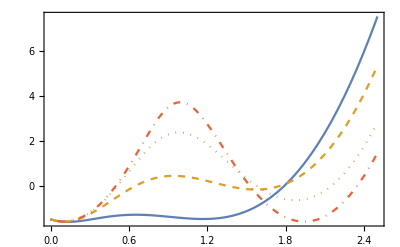

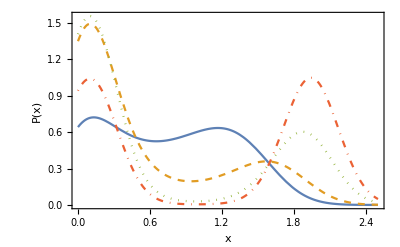

```mathematica
ϕ1=Plot[{ϕ[a[[1]],n[[1]]][x],ϕ[a[[2]],n[[2]]][x],ϕ[a[[3]],n[[3]]][x],ϕ[a[[4]],n[[4]]][x]},{x,0,2.5},Frame->True,PlotStyle->{Line,Dashed,Dotted,DotDashed},FrameTicksStyle->Directive[Black,18]] 
norm1={norma[n[[1]],a[[1]]][x], norma[n[[2]],a[[2]]][x], norma[n[[3]],a[[3]]][x], norma[n[[4]],a[[4]]][x]};
p1=Plot[{P[n[[1]],a[[1]]][x]/norm1[[1]],P[n[[2]],a[[2]]][x]/norm1[[2]],P[n[[3]],a[[3]]][x]/norm1[[3]],P[n[[4]],a[[4]]][x]/norm1[[4]]},{x,0,2.5},Frame->True,PlotStyle->{Line,Dashed,Dotted,DotDashed},AxesLabel->{Style["x",FontSize->16],Style["P(x)",FontSize->16]},FrameTicksStyle->Directive[Black,18]] (*,PlotLegends->{"n=2","n=3","n=5","n=8"}]  *)
```

```mathematica
norm1
```

{6.96943,3.31296,3.17504,4.74645}

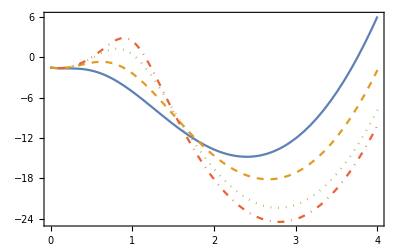

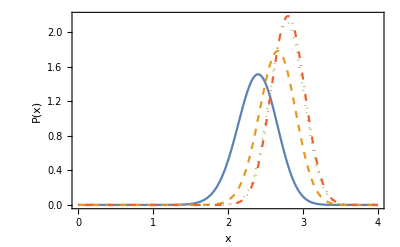

```mathematica
aUp=2.7; (* far from critical value, on upper branch *)
ϕ2=Plot[{ϕ[aUp,n[[1]]][x],ϕ[aUp,n[[2]]][x],ϕ[aUp,n[[3]]][x],ϕ[aUp,n[[4]]][x]},{x,0,4},Frame->True,PlotStyle->{Line,Dashed,Dotted,DotDashed},FrameTicksStyle->Directive[Black,18]] 
norm2=Flatten[{norma[n[[1]],aUp][x], norma[n[[2]],aUp][x], norma[n[[3]],aUp][x], norma[n[[4]],aUp][x]}];
p2=Plot[{P[n[[1]],aUp][x]/norm2[[1]],P[n[[2]],aUp][x]/norm2[[2]],P[n[[3]],aUp][x]/norm2[[3]],P[n[[4]],aUp][x]/norm2[[4]]},{x,0,4},AxesLabel->{Style["x",FontSize->16],Style["P(x)",FontSize->16]},Frame->True,PlotStyle->{Line,Dashed,Dotted,DotDashed},FrameTicksStyle->Directive[Black,18]]
```

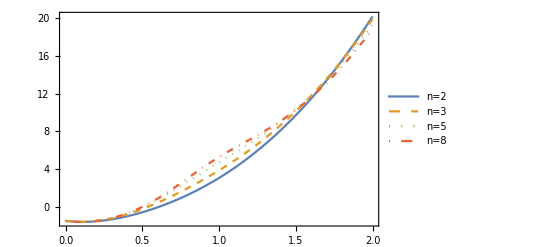

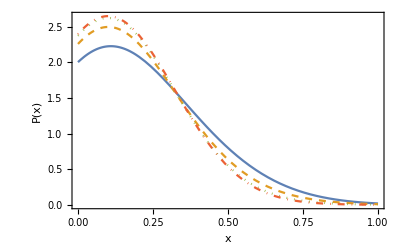

```mathematica
aLow=0.8;
ϕ3=Plot[{ϕ[aLow,n[[1]]][x],ϕ[aLow,n[[2]]][x],ϕ[aLow,n[[3]]][x],ϕ[aLow,n[[4]]][x]},{x,0,2},PlotLegends->Placed[LineLegend[{"n=2","n=3","n=5","n=8"},LabelStyle->{GrayLevel[0.2],25},LegendLayout->{"Row",2}],{0.35,0.75}],Frame->True,PlotStyle->{Line,Dashed,Dotted,DotDashed},FrameTicksStyle->Directive[Black,18]] 
norm3={norma[n[[1]],aLow][x], norma[n[[2]],aLow][x], norma[n[[3]],aLow][x], norma[n[[4]],aLow][x]};
p3=Plot[{P[n[[1]],aLow][x]/norm3[[1]],P[n[[2]],aLow][x]/norm3[[2]],P[n[[3]],aLow][x]/norm3[[3]],P[n[[4]],aLow][x]/norm3[[4]]},{x,0,1},AxesLabel->{Style["x",FontSize->16],Style["P(x)",FontSize->16]},Frame->True,PlotStyle->{Line,Dashed,Dotted,DotDashed},FrameTicksStyle->Directive[Black,18]]
```

## Check for loops in the solutions (representative of stable states) -> Plot the phase space P(x) and P’(x)

### Putting all plots together

#### Middle values

```mathematica
D[P[n[[1]],a[[1]]][x],x];
```

```mathematica
D[P[n[[2]],a[[2]]][x],x];
```

```mathematica
D[P[n[[3]],a[[3]]][x],x];
```

```mathematica
D[P[n[[4]],a[[4]]][x],x]
```

20. ⅇ^(1.49787+20. (0.1 x-x^2/2+0.205556 x^9 Hypergeometric2F1[1,9/8,17/8,-x^8])) (0.1-x+1.85 x^8 (1/(1+x^8)-Hypergeometric2F1[1,9/8,17/8,-x^8])+1.85 x^8 Hypergeometric2F1[1,9/8,17/8,-x^8])

```mathematica
phase1=ParametricPlot[{P[n[[1]],a[[1]]][x]/norm1[[1]],20. ⅇ^(1.4978661367769954+20. (0.1 x-x^2/2+1.85 (x-ArcTan[x]))) (0.1-x+1.85 (1-1/(1+x^2)))/norm1[[1]]},{x,0,3},PlotRange->All,AspectRatio->1,ImageSize->Medium,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->16]]  ;
```

```mathematica
phase2=ParametricPlot[{P[n[[2]],a[[2]]][x]/norm1[[1]],20. ⅇ^(1.4978661367769954+20. (0.1 x-x^2/2+0.4625 x^4 Hypergeometric2F1[1,4/3,7/3,-x^3])) (0.1-x+1.85 x^3 (1/(1+x^3)-Hypergeometric2F1[1,4/3,7/3,-x^3])+1.85 x^3 Hypergeometric2F1[1,4/3,7/3,-x^3])/norm1[[1]]},{x,0,3},PlotRange->All,AspectRatio->1,ImageSize->Medium,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->16],PlotStyle->{ColorData[97,"ColorList"][[2]],Directive[Dashed]}]  ;
```

```mathematica
phase3=ParametricPlot[{P[n[[3]],a[[3]]][x]/norm1[[1]],20. ⅇ^(1.4978661367769954+20. (0.1 x-x^2/2+0.30833333333333335 x^6 Hypergeometric2F1[1,6/5,11/5,-x^5])) (0.1-x+1.85 x^5 (1/(1+x^5)-Hypergeometric2F1[1,6/5,11/5,-x^5])+1.85 x^5 Hypergeometric2F1[1,6/5,11/5,-x^5])/norm1[[1]]},{x,0,3},PlotRange->All,AspectRatio->1,ImageSize->Medium,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->16],PlotStyle->{ColorData[97,"ColorList"][[3]],Directive[Dotted]}]  ;
```

```mathematica
phase4=ParametricPlot[{P[n[[4]],a[[4]]][x]/norm1[[1]],20. ⅇ^(1.4978661367769954+20. (0.1 x-x^2/2+0.20555555555555555 x^9 Hypergeometric2F1[1,9/8,17/8,-x^8])) (0.1-x+1.8499999999999999 x^8 (1/(1+x^8)-Hypergeometric2F1[1,9/8,17/8,-x^8])+1.8499999999999999 x^8 Hypergeometric2F1[1,9/8,17/8,-x^8])/norm1[[1]]},{x,0,3},PlotRange->All,AspectRatio->1,ImageSize->Medium,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->16],PlotStyle->{ColorData[97,"ColorList"][[4]],Directive[DotDashed]}]  ;
```

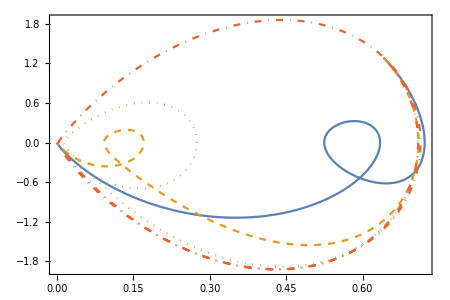

```mathematica
aplot=Show[{phase1,phase2,phase3,phase4},Frame->True,ImageSize->{450,300},AspectRatio->Full]
```

```mathematica
ColorData[97,"ColorList"][[{2,1,3,4,5,6,7,8,9,10}]]
```

{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.]}

#### aUp

```mathematica
D[P[n[[1]],aUp][x],x];
D[P[n[[2]],aUp][x],x];
D[P[n[[3]],aUp][x],x];
D[P[n[[4]],aUp][x],x]
```

20. ⅇ^(1.49787+20. (0.1 x-x^2/2+0.3 x^9 Hypergeometric2F1[1,9/8,17/8,-x^8])) (0.1-x+2.7 x^8 (1/(1+x^8)-Hypergeometric2F1[1,9/8,17/8,-x^8])+2.7 x^8 Hypergeometric2F1[1,9/8,17/8,-x^8])

```mathematica
phase1up=ParametricPlot[{P[n[[1]],aUp][x]/norm2[[1]],20. ⅇ^(1.4978661367769954+20. (0.1 x-x^2/2+2.7 (x-ArcTan[x]))) (0.1-x+2.7 (1-1/(1+x^2)))/norm2[[1]]},{x,0,4},PlotRange->All,AspectRatio->1,ImageSize->Medium,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->16]]  ;
```

```mathematica
phase2up=ParametricPlot[{P[n[[2]],aUp][x]/norm2[[2]],20. ⅇ^(1.4978661367769954+20. (0.1 x-x^2/2+0.675 x^4 Hypergeometric2F1[1,4/3,7/3,-x^3])) (0.1-x+2.7 x^3 (1/(1+x^3)-Hypergeometric2F1[1,4/3,7/3,-x^3])+2.7 x^3 Hypergeometric2F1[1,4/3,7/3,-x^3])/norm2[[2]]},{x,0,4},PlotRange->All,AspectRatio->1,ImageSize->Medium,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->16],PlotStyle->{ColorData[97,"ColorList"][[2]],Directive[Dashed]}]  ;
```

```mathematica
phase3up=ParametricPlot[{P[n[[3]],aUp][x]/norm2[[3]],20. ⅇ^(1.4978661367769954+20. (0.1 x-x^2/2+0.45 x^6 Hypergeometric2F1[1,6/5,11/5,-x^5])) (0.1-x+2.7 x^5 (1/(1+x^5)-Hypergeometric2F1[1,6/5,11/5,-x^5])+2.7 x^5 Hypergeometric2F1[1,6/5,11/5,-x^5])/norm2[[3]]},{x,0,4},PlotRange->All,AspectRatio->1,ImageSize->Medium,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->16],PlotStyle->{ColorData[97,"ColorList"][[3]],Directive[Dotted]}]  ;
```

```mathematica
phase4up=ParametricPlot[{P[n[[4]],aUp][x]/norm2[[4]],20. ⅇ^(1.4978661367769954+20. (0.1 x-x^2/2+0.3 x^9 Hypergeometric2F1[1,9/8,17/8,-x^8])) (0.1-x+2.6999999999999997 x^8 (1/(1+x^8)-Hypergeometric2F1[1,9/8,17/8,-x^8])+2.6999999999999997 x^8 Hypergeometric2F1[1,9/8,17/8,-x^8])/norm2[[4]]},{x,0,4},PlotRange->All,AspectRatio->1,ImageSize->Medium,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->16],PlotStyle->{ColorData[97,"ColorList"][[4]],Directive[DotDashed]}]  ;
```

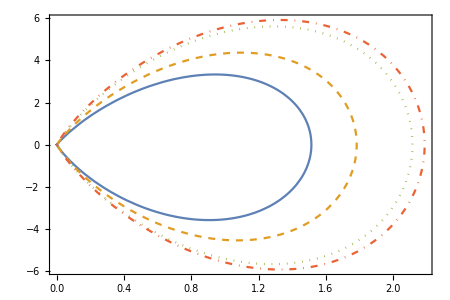

```mathematica
aupplot=Show[{phase1up,phase2up,phase3up,phase4up},Frame->True,ImageSize->{450,300},AspectRatio->Full]
```

#### aLow

```mathematica
D[P[n[[1]],aLow][x],x];
D[P[n[[2]],aLow][x],x];
D[P[n[[3]],aLow][x],x];
D[P[n[[4]],aLow][x],x];
```

```mathematica
phase1low=ParametricPlot[{P[n[[1]],aLow][x]/norm3[[1]],20. ⅇ^(1.4978661367769954+20. (0.1 x-x^2/2+0.8 (x-ArcTan[x]))) (0.1-x+0.8 (1-1/(1+x^2)))/norm3[[1]]},{x,0,4},PlotRange->All,AspectRatio->1,ImageSize->Medium,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->16],PlotLegends->Placed[LineLegend[{Row[{Style["n=2"]}]},LabelStyle->{Black,16,Bold}],Scaled[{0.2,0.9}]]]  ;
```

```mathematica
phase2low=ParametricPlot[{P[n[[2]],aLow][x]/norm3[[2]],20. ⅇ^(1.4978661367769954+20. (0.1 x-x^2/2+0.2 x^4 Hypergeometric2F1[1,4/3,7/3,-x^3])) (0.1-x+0.8 x^3 (1/(1+x^3)-Hypergeometric2F1[1,4/3,7/3,-x^3])+0.8 x^3 Hypergeometric2F1[1,4/3,7/3,-x^3])/norm3[[2]]},{x,0,4},PlotRange->All,AspectRatio->1,ImageSize->Medium,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->16],PlotStyle->{ColorData[97,"ColorList"][[2]],Directive[Dashed]},PlotLegends->Placed[LineLegend[{Row[{Style["n=3"]}]},LabelStyle->{Black,16,Bold}],Scaled[{0.2,0.8}]]]  ;
```

```mathematica
phase3low=ParametricPlot[{P[n[[3]],aLow][x]/norm3[[3]],20. ⅇ^(1.4978661367769954+20. (0.1 x-x^2/2+0.13333333333333333 x^6 Hypergeometric2F1[1,6/5,11/5,-x^5])) (0.1-x+0.8 x^5 (1/(1+x^5)-Hypergeometric2F1[1,6/5,11/5,-x^5])+0.8 x^5 Hypergeometric2F1[1,6/5,11/5,-x^5])/norm3[[3]]},{x,0,4},PlotRange->All,AspectRatio->1,ImageSize->Medium,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->16],PlotStyle->{ColorData[97,"ColorList"][[3]],Directive[Dotted]},PlotLegends->Placed[LineLegend[{Row[{Style["n=5"]}]},LabelStyle->{Black,16,Bold}],Scaled[{0.5,0.9}]]] ;
```

```mathematica
phase4low=ParametricPlot[{P[n[[4]],aLow][x]/norm3[[4]],20. ⅇ^(1.4978661367769954+20. (0.1 x-x^2/2+0.08888888888888889 x^9 Hypergeometric2F1[1,9/8,17/8,-x^8])) (0.1-x+0.8 x^8 (1/(1+x^8)-Hypergeometric2F1[1,9/8,17/8,-x^8])+0.8 x^8 Hypergeometric2F1[1,9/8,17/8,-x^8])/norm3[[4]]},{x,0,4},PlotRange->All,AspectRatio->1,ImageSize->Medium,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->16],PlotStyle->{ColorData[97,"ColorList"][[4]],Directive[DotDashed]},PlotLegends->Placed[LineLegend[{Row[{Style["n=8"]}]},LabelStyle->{Black,16,Bold}],Scaled[{0.5,0.8}]]]  ;
```

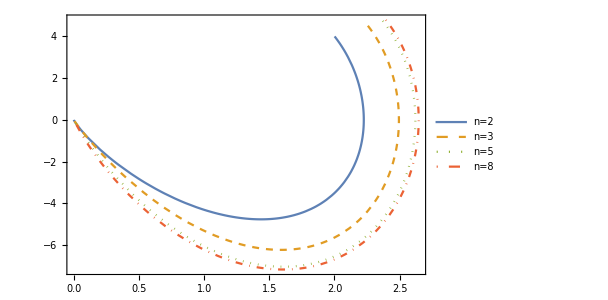

```mathematica
alowplot=Show[{phase1low,phase2low,phase3low,phase4low},Frame->True,ImageSize->{450,300},AspectRatio->Full]
```

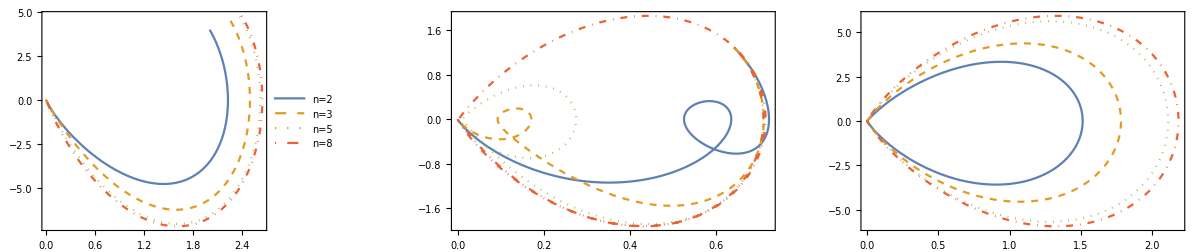
-Graphics-P_s'(x)P_s(x)

```mathematica
Labeled[
GraphicsGrid[{{alowplot,aplot,aupplot}},ImageSize->Full],
{Pane["P_s'(x)"],"P_s(x)",""},{Left,Bottom,Top},RotateLabel->True,LabelStyle->Directive[Bold,FontFamily->"Helvetica",FontSize->18]]
```